```mathematica
CondSweep1[x_]:=Exp[-x^2/alpha2]
CondSweep2[x_]:=Exp[-rho*mu*((c0 π x^3)/(c0-c1)^2+(c0^2 π x^3)/(3 (-c0+c1)^3)-(c1^2 π x^3)/(3 (-c0+c1)^3)+(π x^3)/(-c0+c1))]
CondSweep3[x_]:= Exp[-rho*mu*(-(π x^4)/(3 c0)-(c1^3 π x^4)/(3 (c0-c1)^4)+(c1^4 π x^4)/(3 c0 (c0-c1)^4))]
```

```mathematica
alpha2=(c1-c0)/(rho*mu)
```

(-c0+c1)/(mu rho)

```mathematica
c0=1
c1=2*c0
rho=0.5
mu=10^{-5}
```

1

2

0.5

{1/100000}

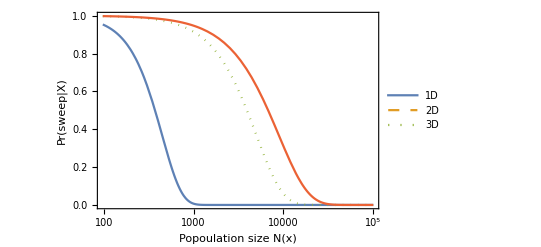

```mathematica
LogLinearPlot[{CondSweep1[x],,CondSweep2[(x/Pi )^{1/2}],CondSweep3[(x*3/(4*Pi))^{1/3}]},{x,0,100000}, Frame->True, PlotStyle-> {Line, Dashed, Dotted},FrameLabel->{Style["Popoulation size N(x)",Bold,12], Style["Pr(sweep|X)",Bold,12]},RotateLabel->True, PlotLegends->Placed[{"1D","2D","3D"},Center]]
```